```mathematica
Clear["Global`*"]
```

This section is mostly not attempted. The problems seem too simplistic to challenge Mathematica. I feel that if difficult eigenvalue problems were to come up, the most efficient approach would likely be entirely different than anything referred to here. By the way, there is a recently discovered (Oct ‘18) bug in the Eigenvalues function , discussed at https://mathematica.stackexchange.com/questions/186224/wrong-eigenvalues-from-a-sparse-matrix-eigenvalues-are-nonreal.  It looks like the Arnoldi method may be at fault, and it might be a good idea to avoid it for now.

If it is necessary to numerically fish for eigenvalues, the QRDecomposition method, treated in section 20.9, is one to consider.

1 - 4 Power method without scaling
Apply the power method without scaling (3 steps), using x_0 = {1,1}^T or {1, 1, 1}^T . Give Rayleigh quotients and error bounds.

1.  (9 | 4
4 | 3)

```mathematica
m1=({{9, 4}, {4, 3}})
```

{{9,4},{4,3}}

```mathematica
Eigenvalues[m1]
```

{11,1}

Just to blow out the cobwebs, let me try a couple of fairly large ones.

```mathematica
m30=Table[RandomSample[Range[40],30],{n,1,30}];
```

```mathematica
m30p=Table[m30[[n]](-1)^m30[[n]],{n,1,30}];
```

Mathematica has no difficulty in finding eigenvalues of relatively sizeable matrices. Reviewing the suggested techniques in the documentation would serve better, probably, than trying out the limited approaches described in this section.

```mathematica
Timing[N[Eigenvalues[m30p]]]
```

{0.301897,{123.43+38.8128 ⅈ,123.43-38.8128 ⅈ,-77.3667+93.2068 ⅈ,-77.3667-93.2068 ⅈ,15.5139+118.638 ⅈ,15.5139-118.638 ⅈ,-107.456,73.5353+73.4756 ⅈ,73.5353-73.4756 ⅈ,-82.818+49.6166 ⅈ,-82.818-49.6166 ⅈ,-45.9606+82.8799 ⅈ,-45.9606-82.8799 ⅈ,94.5401,43.3048+78.365 ⅈ,43.3048-78.365 ⅈ,-72.1173+21.2722 ⅈ,-72.1173-21.2722 ⅈ,66.5277+30.0296 ⅈ,66.5277-30.0296 ⅈ,-13.1193+68.3912 ⅈ,-13.1193-68.3912 ⅈ,-46.1061+26.1212 ⅈ,-46.1061-26.1212 ⅈ,25.2435+39.9165 ⅈ,25.2435-39.9165 ⅈ,36.3336+16.044 ⅈ,36.3336-16.044 ⅈ,-12.9431+7.80501 ⅈ,-12.9431-7.80501 ⅈ}}

The eigenvalues of a random symmetric matrix:

```mathematica
r=RandomReal[1,{100,100}];
r=Transpose[r].r;
vals= Timing[Eigenvalues[r]];
```

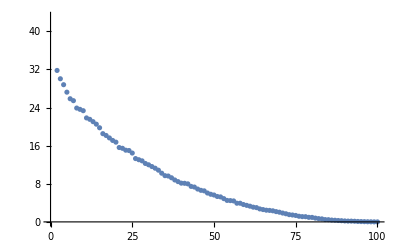

```mathematica
ListPlot[vals]
```

3.  (2 | -1 | 1
-1 | 3 | 2
1 | 2 | 3)

```mathematica
Clear["Global`*"]
```

```mathematica
m1=({{2, -1, 1}, {-1, 3, 2}, {1, 2, 3}})
```

{{2,-1,1},{-1,3,2},{1,2,3}}

```mathematica
Eigenvalues[m1]
```

{5,3,0}

5 - 8 Power method with scaling
Apply the power method (3 steps) with scaling, using x_0 = {1, 1, 1}^T or {1, 1, 1, 1}^T , as applicable. Give Raleigh quotients and error bounds.

5.  The matrix in problem 3.

7.  (5 | 1 | 0 | 0
1 | 3 | 1 | 0
0 | 1 | 3 | 1
0 | 0 | 1 | 5)

```mathematica
m1=({{5, 1, 0, 0}, {1, 3, 1, 0}, {0, 1, 3, 1}, {0, 0, 1, 5}})
```

{{5,1,0,0},{1,3,1,0},{0,1,3,1},{0,0,1,5}}

```mathematica
N[Eigenvalues[m1]]
```

{5.61803,5.30278,3.38197,1.69722}

The above match the text answer to 4S.

9.  Prove that if x is an eigenvector, the δ = 0 in (2). Give two examples.

11. Spectral shift, smallest eigenvalue. In problem 3, set B = A - 3 ⅈ  (as perhaps suggested by the diagonal entries) and see whether you may get a sequence of q’s converging to an eigenvalue of A that is smallest (not largest) in absolute value. Use x_0 = {1, 1, 1}^T. Do 8 steps. Verify that A has the spectrum {0, 3, 5}.